## Day 1: No Time for a Taxicab

http://adventofcode.com/2016/day/1

How many blocks away is Easter Bunny HQ?

```mathematica
input="R4, R1, L2, R1, L1, L1, R1, L5, R1, R5, L2, R3, L3, L4, R4, R4, R3, L5, L1, R5, R3, L4, R1, R5, L1, R3, L2, R3, R1, L4, L1, R1, L1, L5, R1, L2, R2, L3, L5, R1, R5, L1, R188, L3, R2, R52, R5, L3, R79, L1, R5, R186, R2, R1, L3, L5, L2, R2, R4, R5, R5, L5, L4, R5, R3, L4, R4, L4, L4, R5, L4, L3, L1, L4, R1, R2, L5, R3, L4, R3, L3, L5, R1, R1, L3, R2, R1, R2, R2, L4, R5, R1, R3, R2, L2, L2, L1, R2, L1, L3, R5, R1, R4, R5, R2, R2, R4, R4, R1, L3, R4, L2, R2, R1, R3, L5, R5, R2, R5, L1, R2, R4, L1, R5, L3, L3, R1, L4, R2, L2, R1, L1, R4, R3, L2, L3, R3, L2, R1, L4, R5, L1, R5, L2, L1, L5, L2, L5, L2, L4, L2, R3";
```

```mathematica
directions={StringTake[#,1],ToExpression@StringTake[#,-StringLength@#+1]}&/@StringSplit[StringReplace[input," "->""],","];
```

```mathematica
applyDir[{{p_,v_},n_}]:=Module[{vnew},
vnew=RotationMatrix[Switch[directions⟦n,1⟧,"R",-π/2,"L",π/2]].v;
{{p+vnew directions⟦n,2⟧,vnew},n+1}
]
```

```mathematica
path=NestList[applyDir,{{{0,0},{-1,0}},1},Length@directions];
```

```mathematica
path[[-1,1,1]]
```

{113,-48}

```mathematica
Norm[path[[-1,1,1]],1]
```

161

Correct answer: 161

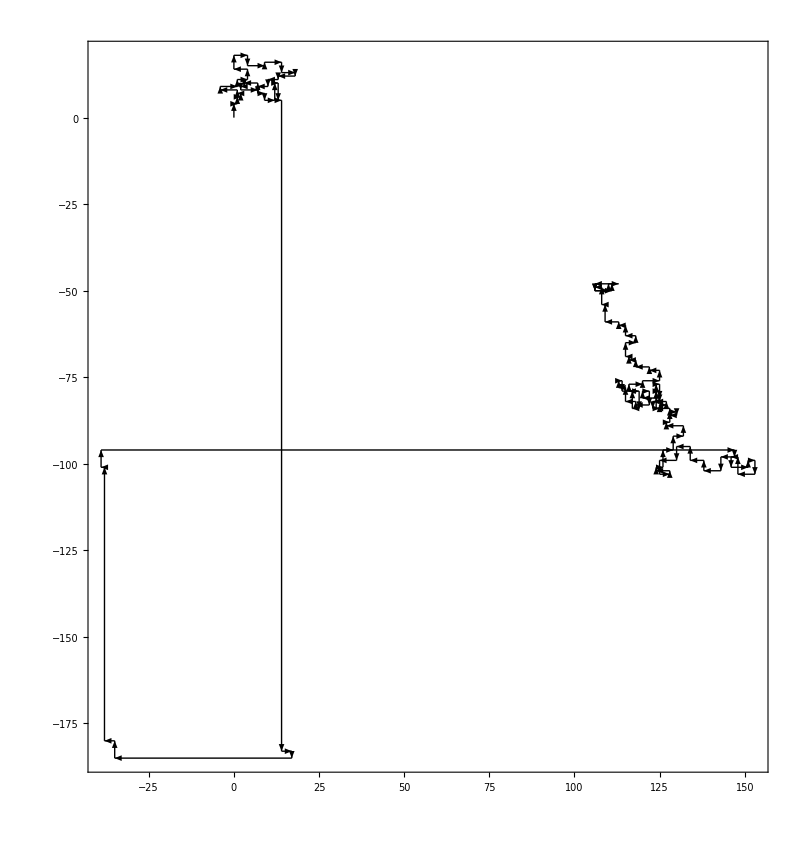

```mathematica
Graphics[{Arrowheads[0.001],Arrow/@Partition[path[[All,1,1]],2,1]},ImageSize->800,Frame->True]
```

### Part 2: extract first location visited twice

```mathematica
Norm[{14,-96},1]
```

110